```mathematica
Needs["Dielectrics`"]
Needs["Constants`"]
Needs["Utilities`"]
```

## Extract Data, Fit Drude, Save Parameters

Whether or not to plot fits (plotting significantly slows down run times)

```mathematica
PLOT = False;
```

### Iron

This data is taken from a book of optical measurments by Palik (https://doi.org/10.1016/B978-012544415-6.50000-5 )

Data was extracted from Screenshots of tables in the book using  https://www.docsumo.com/free-tools/extract-tables-from-pdf-images

#### Import Data

```mathematica
opticaliron1 = Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_1.csv"][[2;;,;;3]];
opticaliron2 = Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_2.csv"][[2;;,;;3]];
opticaliron3 = ToExpression[Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_3.csv"][[2;;,;;3]]];
```

#### Assign to variables

```mathematica
kFe= Join[opticaliron1[[;;,3]],opticaliron2[[;;,3]],opticaliron3[[;;,3]]]; (*[]*)
nFe= Join[opticaliron1[[;;,2]],opticaliron2[[;;,2]],opticaliron3[[;;,2]]]; (*[]*)
ωFe= Join[opticaliron1[[;;,1]],opticaliron2[[;;,1]],opticaliron3[[;;,1]]]; (*[eV]*)
```

#### Convert to ϵ

The following relation between k, n and ϵ where given in Palik

```mathematica
ϵFe = ComplexExpand[nFe^2- kFe^2 + 2 I nFe kFe] ;
ELFFe = Im[-1/ϵFe];
```

```mathematica
ELFFeData = Table[{ωFe[[i]],ELFFe[[i]]},{i,Length[ωFe]}];
logELFFeData =Table[{Log[10,ωFe[[i]]],ELFFe[[i]]},{i,Length[ωFe]}];
loglogELFFeData =Table[{Log[10,ωFe[[i]]],N[Log10[ELFFe[[i]]]]},{i,Length[ωFe]}];
```

```mathematica
(*ListPlot[logELFFeData,PlotRange->All]
ListPlot[loglogELFFeData,PlotRange->All]*)
```

```mathematica
fFe=Interpolation[logELFFeData]
(*Plot[fFe[ω],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All]*)
```

InterpolatingFunction[…]

#### Find Maxima

{{37,-0.376743},{64,-2.42196},{87,-2.02921},{96,-5.07569},{140,-0.32904},{186,-0.0970295},{210,-0.171178},{286,-0.055882}}

{{1.77262,-0.376743},{2.85618,-2.42196},{2.44483,-2.02921},{3.85956,-5.07569},{1.02531,-0.32904},{1.31806,-0.0970295},{1.20412,-0.171178},{1.37291,-0.055882}}

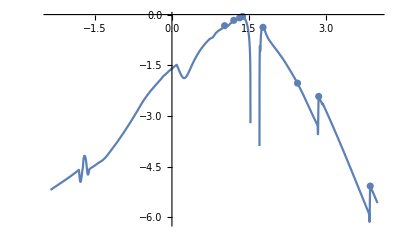

{{1.02531,-0.32904},{1.20412,-0.171178},{1.37291,-0.055882},{1.77262,-0.376743},{2.85618,-2.42196},{3.85956,-5.07569}}

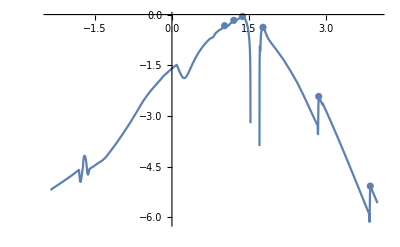

```mathematica
FindPeaks[loglogELFFeData[[;;,2]]]
FePeaks = Table[N[loglogELFFeData[[Round[%[[i]][[1]]]]]],{i,Length[%]}]
Show[{Plot[Log10[fFe[ω]],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All],ListPlot@FePeaks}]
FePeaks = SortBy[N[Delete[FePeaks,{{3},{6}}]],First]
Show[{Plot[Log10[fFe[ω]],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All],ListPlot@FePeaks}]
```

#### Fit drude functions with truncation

```mathematica
AsFe={A1,A2,A3,A4,A5,A6};
νsFe = {ν1,ν2,ν3,ν4,ν5,ν6};
(*FePeaksToFit = {3,6,7,8};*)
(*ωedgesFe = {(fFe@Domain)[[1,1]],(fFe@Domain)[[1,1]],(fFe@Domain)[[1,1]],FePeaks[[4,1]],FePeaks[[5,1]]};*)
ωedgesFe = {-0.4,(fFe@Domain)[[1,1]],-0.7,-1,FePeaks[[5,1]],FePeaks[[6,1]]};
FeFit=NonlinearModelFit[SortBy[ELFFeData,First],Sum[AsFe[[i]] ELFM0[ω,νsFe[[i]],ωi[10^FePeaks[[i,1]],νsFe[[i]]]]HeavisideTheta[ω-10^ωedgesFe[[i]]],{i,Length[FePeaks]}],Join[AsFe,νsFe],ω]

FeFit["BestFitParameters"]
FeFit["ParameterTable"]
FeFit["ANOVATable"](*error MS is χ^2/ndof*)
```

FittedModel[(537992. ω (1.18157×10^7+ω^2) HeavisideTheta[-7237.+ω])/(1.3961×10^14 (5.23742×10^7+ω^2)+«1» «1»+1.18157×10^7 («22»-«22» «1»+2. ω^4))+(«1»)/(«1»)+«2»+(«1»)/(«1»)+(«1»)/(«1»)]

{A1→0.209474,A2→0.0699144,A3→0.386622,A4→0.234383,A5→0.00193079,A6→2.83087×10^-6,ν1→11.5323,ν2→5.92674,ν3→13.2953,ν4→61.3004,ν5→487.855,ν6→3437.39}

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 0.209474 | 0.0115459 | 18.1427 | 1.55872×10^-49
A2 | 0.0699144 | 0.0127074 | 5.50188 | 8.32595×10^-8
A3 | 0.386622 | 0.0229633 | 16.8365 | 1.0227×10^-44
A4 | 0.234383 | 0.00802579 | 29.2037 | 6.06932×10^-88
A5 | 0.00193079 | 0.00787429 | 0.245202 | 0.806475
A6 | 2.83087×10^-6 | 0.00878561 | 0.000322216 | 0.999743
ν1 | 11.5323 | 0.819577 | 14.071 | 1.47178×10^-34
ν2 | 5.92674 | 0.680342 | 8.71142 | 2.42906×10^-16
ν3 | 13.2953 | 0.786661 | 16.9009 | 5.91886×10^-45
ν4 | 61.3004 | 3.44085 | 17.8155 | 2.50062×10^-48
ν5 | 487.855 | 3022.46 | 0.16141 | 0.871884
ν6 | 3437.39 | 1.42811×10^7 | 0.000240695 | 0.999808

| DF | SS | MS
Model | 12 | 42.9893 | 3.58244
Error | 287 | 0.131253 | 0.000457328
Uncorrected Total | 299 | 43.1205 | 
Corrected Total | 298 | 27.5345 |

```mathematica
If[PLOT,Show[{Plot[Log10[Sum[AsFe[[i]] ELFM0[10^ω,νsFe[[i]],ωi[10^FePeaks[[i,1]],νsFe[[i]]]]HeavisideTheta[ω-ωedgesFe[[i]]],{i,Length[AsFe]}]/.FeFit["BestFitParameters"]],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]] []"],ListPlot[Log10[SortBy[ELFFeData,First]]]}]]
```

```mathematica
If[PLOT,Show[Table[Plot[Log10[AsFe[[i]] ELFM0[10^ω,νsFe[[i]],ωi[10^FePeaks[[i,1]],νsFe[[i]]]]HeavisideTheta[ω-ωedgesFe[[i]]]]/.FeFit["BestFitParameters"],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)"],{i,Length[FePeaks]}]]]
```

### MgO

#### Extract Data from Images

Optical (q=0) plots from https://journals.aps.org/prb/abstract/10.1103/PhysRevB.48.4373

```mathematica
(*i=-Graphics-*)
```

courtesy of https://mathematica.stackexchange.com/questions/246408/digitise-curves-from-an-existing-plot-image

```mathematica
(*ic=SelectComponents[ColorNegate[MorphologicalBinarize[i,.6]],Large]
d=Pruning[MorphologicalTransform[Thinning@Pruning[ic,10],"Bridge"],10]*)
```

```mathematica
(*i2=d-MorphologicalTransform[d,{"SkeletonBranchPoints"}]*)
```

```mathematica
(*Colorize[MorphologicalComponents[i2]]*)
```

```mathematica
(*components=MorphologicalComponents[ImageCrop@i2];*)
```

```mathematica
(*plots=(ColorNegate@Image@#&/@Table[(components/. {n->1,_Integer->0}),{n,Union[Flatten@components][[2;;]]}]);*)
```

```mathematica
(*plots[[43]]*)
```

```mathematica
(*plots[[35]]*)
```

```mathematica
(*plots[[37]]*)
```

```mathematica
(*plots[[38]]*)
```

```mathematica
(*plots[[40]]*)
```

```mathematica
(*Dimensions[components]*)
```

```mathematica
(*pd=Table[(components/. {n->1,_Integer->0}),{n,Union[Flatten@components][[2;;]]}];

pd = {pd[[35]],pd[[37]],pd[[38]],pd[[40]],pd[[43]]}
(*,pd[[44]]}*)

rescaled=SubsetMap[Rescale[#,{0,(Dimensions[pd][[3]])/75}]&,SubsetMap[Rescale[#,{0,Dimensions[pd][[2]]}/4]&,Position[Transpose@Reverse@#,1],{All,2}],{All,1}]&/@pd;
*)
```

```mathematica
(*pd=Table[(components/. {n->1,_Integer->0}),{n,Union[Flatten@components][[2;;]]}][[28;;49]];

rescaled=SubsetMap[Rescale[#,{0,(Dimensions[pd][[3]])/2000}]&,SubsetMap[Rescale[#,{0,Dimensions[pd][[2]]}/2]&,Position[Transpose@Reverse@#,1],{All,2}],{All,1}]&/@pd;*)
```

```mathematica
(*ListLinePlot@rescaled*)
```

```mathematica
(*ListPlot@Join[rescaled[[1]],rescaled[[2]],rescaled[[3]],rescaled[[4]],{{0,0}}]*)
```

#### Interpolate

add origin and midpoint between origin and left most point to help interpolation

```mathematica
(*MgOData=Join[rescaled[[1]],rescaled[[2]],rescaled[[3]],rescaled[[4]],rescaled[[5]],{{0,0}}];
SortBy[MgOData,First];
Midpoint[{%[[1]],%[[2]] }];
MgOData = AppendTo[MgOData,%];
*)
```

```mathematica
(**)
```

```mathematica
(*MgOData=DeleteDuplicatesBy[MgOData,First];
Length[MgOData]
fMgO=Interpolation[MgOData]
Plot[fMgO[ω],{ω,0,(fMgO@Domain)[[1,2]]},PlotRange->All]*)
```

#### Save extracted data to file

```mathematica
(*SaveIt[NotebookDirectory[]<>"MgOData",MgOData]
SaveIt[NotebookDirectory[]<>"fMgO",fMgO]*)
```

```mathematica
(*NotebookDirectory[]*)
```

#### find maxima - Load Data

```mathematica
Clear[fMgO]
MgOData = ReadIt[NotebookDirectory[]<>"MgOData"];
fMgO[ω_] := ReadIt[NotebookDirectory[]<>"fMgO"][ω]
fMgOdomain = (ReadIt[NotebookDirectory[]<>"fMgO"]@Domain)
```

{{0,54675/737}}

```mathematica
(*ListPlot[MgOData]
Plot[fMgO[x],{x,0,70},PlotRange->All]*)
```

```mathematica
FindPeaks[MgOData[[;;,2]]];
MgOPeaks = Table[MgOData[[Round[%[[i]][[1]]]]],{i,Length[%]}];
MgOPeaks = Delete[SortBy[MgOPeaks,First],{{1},{8},{10},{12},{13},{14},{15},{16},{18},{19},{20},{21}}]
(*Show[{Plot[fMgO[ω],{ω,0,fMgOdomain[[1,2]]},PlotRange->All],ListPlot@MgOPeaks}]*)
```

{{6000/737,108/773},{8625/737,252/773},{10575/737,372/773},{11325/737,392/773},{15150/737,824/773},{16350/737,1532/773},{18075/737,1080/773},{24825/737,328/773},{42375/737,192/773}}

#### fit optical mermin functions to peaks

Now with fixed peak position

Using truncation and results of improvements below

```mathematica
AsMgO={A1,A2,A3,A4};
νsMgO = {ν1,ν2,ν3,ν4};
MgOPeaksToFit = {3,6,7,8};
ωedgesMgO = {0,0,0,0};
MgOFit=NonlinearModelFit[MgOData,Sum[AsMgO[[i]] ELFM0[ω,νsMgO[[i]],ωi[MgOPeaks[[MgOPeaksToFit[[i]],1]],νsMgO[[i]]]]HeavisideTheta[ω-ωedgesMgO[[i]]],{i,Length[AsMgO]}],Join[AsMgO,νsMgO],ω];
MgOFit["BestFitParameters"]
MgOFit["ParameterTable"]
MgOFit["ANOVATable"](* error MS is χ^2/ndof*)
```

{A1→0.039834,A2→0.180092,A3→0.0963866,A4→0.421157,ν1→2.79888,ν2→3.33721,ν3→3.44427,ν4→74.0193}

General::munfl: Exp[-825.622] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 0.039834 | 0.00356021 | 11.1887 | 1.01232×10^-26
A2 | 0.180092 | 0.00460464 | 39.1108 | 1.05314×10^-173
A3 | 0.0963866 | 0.00434513 | 22.1827 | 8.36692×10^-82
A4 | 0.421157 | 0.00490583 | 85.8484 | 0.
ν1 | 2.79888 | 0.333219 | 8.39952 | 2.76451×10^-16
ν2 | 3.33721 | 0.0854008 | 39.0771 | 1.56619×10^-173
ν3 | 3.44427 | 0.142759 | 24.1265 | 1.38816×10^-92
ν4 | 74.0193 | 2.70296 | 27.3845 | 9.85095×10^-111

| DF | SS | MS
Model | 8 | 164.653 | 20.5816
Error | 657 | 1.72104 | 0.00261955
Uncorrected Total | 665 | 166.374 | 
Corrected Total | 664 | 72.8206 |

```mathematica
If[PLOT,Show[{Plot[fMgO[ω],{ω,0,fMgOdomain[[1,2]]},PlotRange->All,AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_MgO](ω)"],Plot[Sum[AsMgO[[i]] ELFM0[ω,νsMgO[[i]],ωi[MgOPeaks[[MgOPeaksToFit[[i]],1]],νsMgO[[i]]]]HeavisideTheta[ω-ωedgesMgO[[i]]],{i,Length[AsMgO]}]/.MgOFit["BestFitParameters"],{ω,0,fMgOdomain[[1,2]]},PlotRange->All]}]]
```

```mathematica
(*Show[{Plot[Log10[fMgO[10^ω]],{ω,0.8,Log10[fMgOdomain[[1,2]]]},PlotRange->All,AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_MgO](ω)"],Plot[Log10[Sum[AsMgO[[i]] ELFM0[10^ω,νsMgO[[i]],ωi[MgOPeaks[[MgOPeaksToFit[[i]],1]],νsMgO[[i]]]]HeavisideTheta[10^ω-ωedgesMgO[[i]]],{i,Length[AsMgO]}]/.MgOFit["BestFitParameters"]],{ω,0.8,Log10[fMgOdomain[[1,2]]]},PlotRange->All,PlotStyle->Orange]}]*)
```

### SiO_2

#### get data

```mathematica
(**)
```

also try https://reference.wolfram.com/language/howto/GetCoordinatesForPointsInAPlot.html
https://reference.wolfram.com/language/tutorial/InteractiveGraphicsPalette.html

```mathematica
(*i=-Graphics-*)
```

```mathematica
(*ic=SelectComponents[ColorNegate[MorphologicalBinarize[i,.6]],Large]
d=Pruning[MorphologicalTransform[Thinning@Pruning[ic,10],"Bridge"],10]*)
```

```mathematica
(*i2=d-MorphologicalTransform[d,{"SkeletonBranchPoints"}];
Colorize[MorphologicalComponents[i2]]*)
```

```mathematica
(*components=MorphologicalComponents[ImageCrop@i2];*)
```

```mathematica
(*plots=(ColorNegate@Image@#&/@Table[(components/. {n->1,_Integer->0}),{n,Union[Flatten@components][[2;;]]}]);*)
```

```mathematica
(*plots[[30]]*)
```

```mathematica
(*plots[[35]]*)
```

```mathematica
(*plots[[36]]*)
```

```mathematica
(*plots[[39]]*)
```

```mathematica
(*plots[[43]]*)
```

```mathematica
(*plots;*)
```

```mathematica
(*pd=Table[(components/. {n->1,_Integer->0}),{n,Union[Flatten@components][[2;;]]}];

pd = {pd[[30]],pd[[35]],pd[[36]],pd[[39]],pd[[43]]}
(*,pd[[44]]}*)

rescaled=SubsetMap[Rescale[#,{0,(Dimensions[pd][[3]])/100}]&,SubsetMap[Rescale[#,{0,Dimensions[pd][[2]]}/2]&,Position[Transpose@Reverse@#,1],{All,2}],{All,1}]&/@pd;
*)
```

```mathematica
(*ListLinePlot@rescaled
ListPlot@Join[rescaled[[1]],rescaled[[2]],rescaled[[3]],rescaled[[4]],rescaled[[5]],{{0,0}}]*)
```

Remove bar at bottom, add in midpoint

```mathematica
(*SiO2Data=Join[rescaled[[1]],rescaled[[2]],rescaled[[3]],rescaled[[4]],rescaled[[5]],{{0,0}}];
SiO2Data=Select[SiO2Data,Last[#]>5/193|| Last[#]<1/386&];
SiO2Data=Select[SiO2Data,First[#]!=43600/727&];
SiO2Data=Select[SiO2Data,First[#]!=58100/727&];
SortBy[SiO2Data,First];
Midpoint[{%[[1]],%[[2]] }];
SiO2Data = AppendTo[SiO2Data,%];
SortBy[SiO2Data,First];
Midpoint[{%[[2]],%[[3]] }];
SiO2Data = AppendTo[SiO2Data,%];
SortBy[SiO2Data,First];
Midpoint[{%[[3]],%[[4]] }];
SiO2Data = AppendTo[SiO2Data,%];*)
```

Remove bar at bottom

```mathematica
(**)
```

```mathematica
(*ListPlot@SiO2Data*)
```

```mathematica
(*60 727
80 727*)
```

```mathematica
(*SiO2Data=DeleteDuplicatesBy[SiO2Data,First];
ListPlot@SiO2Data*)
```

```mathematica
(*
Length[SiO2Data]
fSiO2=Interpolation[SiO2Data]
Plot[fSiO2[ω],{ω,0,(fSiO2@Domain)[[1,2]]},PlotRange->All]*)
```

```mathematica
(*SaveIt[NotebookDirectory[]<>"SiO2Data",SiO2Data]
SaveIt[NotebookDirectory[]<>"fSiO2",fSiO2]*)
```

#### Find extrema - Load Data

```mathematica
SiO2Data = ReadIt[NotebookDirectory[]<>"SiO2Data"];
fSiO2[ω_] := ReadIt[NotebookDirectory[]<>"fSiO2"][ω]
fSiO2Domain = (ReadIt[NotebookDirectory[]<>"fSiO2"]@Domain)
```

{{0,72400/727}}

```mathematica
FindPeaks[SiO2Data[[;;,2]]];
SiO2Peaks = Table[SiO2Data[[Round[%[[i]][[1]]]]],{i,Length[%]}];
SiO2Peaks = Delete[SortBy[SiO2Peaks,First],{{1},{7},{9},{10},{11}}]
(*Show[{Plot[fSiO2[ω],{ω,0,(fSiO2Domain)[[1,2]]},PlotRange->All],ListPlot@SiO2Peaks}]*)
```

{{9300/727,66/193},{11100/727,187/386},{16500/727,383/386},{28200/727,48/193},{35600/727,35/193},{51400/727,29/386}}

#### Fit the Optical Mermin function

Try again with truncation

```mathematica
(*As={A1,A2};
νs = {ν1,ν2};
SiO2PeaksToFit = {3,5};
ωedges = {10.5,0};
SiO2Fit=NonlinearModelFit[SiO2Data,Sum[As[[i]] ELFM0[ω,νs[[i]],ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νs[[i]]]]HeavisideTheta[ω-ωedges[[i]]],{i,Length[As]}],Join[As,νs],ω];
Show[{Plot[fSiO2[ω],{ω,0,(fSiO2@Domain)[[1,2]]},PlotRange->All],Plot[Sum[As[[i]] ELFM0[ω,νs[[i]],ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νs[[i]]]]HeavisideTheta[ω-ωedges[[i]]],{i,Length[As]}]/.SiO2Fit["BestFitParameters"],{ω,0,(fSiO2@Domain)[[1,2]]},PlotRange->All]}]
SiO2Fit["BestFitParameters"]
SiO2Fit["ParameterTable"]
SiO2Fit["ANOVATable"](*error MS is χ^2/ndof*)*)
```

And without and with statistics

```mathematica
AsSiO2={A1,A2};
νsSiO2 = {ν1,ν2};
SiO2PeaksToFit = {3,5};
(*ωedges = {10.5,0};*)
ωedgesSiO2 = {0,0};
SiO2Fit=NonlinearModelFit[SiO2Data,Sum[AsSiO2[[i]] ELFM0[ω,νsSiO2[[i]],ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νsSiO2[[i]]]]HeavisideTheta[ω-ωedgesSiO2[[i]]],{i,Length[AsSiO2]}],Join[AsSiO2,νsSiO2],ω];
SiO2Fit["BestFitParameters"]
SiO2Fit["ParameterTable"]
SiO2Fit["ANOVATable"](*error MS is χ^2/ndof*)
```

{A1→0.552697,A2→0.0871584,ν1→13.9306,ν2→39.9104}

General::munfl: Exp[-1130.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-945.403] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 0.552697 | 0.00371722 | 148.686 | 0.
A2 | 0.0871584 | 0.00280535 | 31.0686 | 4.49529×10^-129
ν1 | 13.9306 | 0.127249 | 109.476 | 0.
ν2 | 39.9104 | 1.91102 | 20.8844 | 5.95481×10^-74

| DF | SS | MS
Model | 4 | 83.4234 | 20.8559
Error | 628 | 0.566721 | 0.000902422
Uncorrected Total | 632 | 83.9901 | 
Corrected Total | 631 | 46.0465 |

```mathematica
If[PLOT,Show[{Plot[fSiO2[ω],{ω,0,(fSiO2Domain)[[1,2]]},PlotRange->All],Plot[Sum[AsSiO2[[i]] ELFM0[ω,νsSiO2[[i]],ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νsSiO2[[i]]]]HeavisideTheta[ω-ωedgesSiO2[[i]]],{i,Length[AsSiO2]}]/.SiO2Fit["BestFitParameters"],{ω,0,(fSiO2Domain)[[1,2]]},PlotRange->All]},AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_SiO2](ω)"]]
```

```mathematica
(*Show[{Plot[Log10[fSiO2[ω]],{ω,0,(fSiO2Domain)[[1,2]]},PlotRange->All],Plot[Log10[Sum[AsSiO2[[i]] ELFM0[ω,νsSiO2[[i]],ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νsSiO2[[i]]]]HeavisideTheta[ω-ωedgesSiO2[[i]]],{i,Length[AsSiO2]}]]/.SiO2Fit["BestFitParameters"],{ω,0,(fSiO2Domain)[[1,2]]},PlotRange->All]},AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_SiO2](ω)"]*)
```

```mathematica
(*ωedges = {0,0};
Show[{Plot[Log10[fSiO2[10^ω]],{ω,0.7,Log10[(fSiO2Domain)[[1,2]]]},PlotRange->All],Plot[Log10[Sum[AsSiO2[[i]] ELFM0[10^ω,νsSiO2[[i]],ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νsSiO2[[i]]]]HeavisideTheta[10^ω-ωedges[[i]]],{i,Length[AsSiO2]}]]/.SiO2Fit["BestFitParameters"],{ω,0.7,Log10[(fSiO2Domain)[[1,2]]]},PlotRange->All,PlotStyle->Orange]},AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_SiO2](ω)"]*)
```

```mathematica
(*ωedges = {10.5,0};
Show[{Plot[Log10[fSiO2[10^ω]],{ω,0,Log10[(fSiO2Domain)[[1,2]]]},PlotRange->All],Plot[Log10[Sum[AsSiO2[[i]] ELFM0[10^ω,νsSiO2[[i]],ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νsSiO2[[i]]]]HeavisideTheta[10^ω-ωedges[[i]]],{i,Length[AsSiO2]}]]/.SiO2Fit["BestFitParameters"],{ω,0,Log10[(fSiO2Domain)[[1,2]]]},PlotRange->All,PlotStyle->Orange]},AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_SiO2](ω)"]*)
```

```mathematica
(*Table[N[SiO2Peaks[[SiO2PeaksToFit[[i]],1]]],{i,2}]*)
```

```mathematica
(*SaveIt[NotebookDirectory[]<>"SiO2Fit",SiO2Fit]
SaveIt[NotebookDirectory[]<>"SiO2PeaksToFit",SiO2PeaksToFit]
SaveIt[NotebookDirectory[]<>"SiO2Peaks",SiO2Peaks]*)
```

### Calculate and save parameter replacement tables

#### Iron - w crust temperatures

```mathematica
Feparameters = Table[{ωi->JpereV/hbar ωi[10^FePeaks[[i,1]],νsFe[[i]]],νi->JpereV/hbar νsFe[[i]],Ai->AsFe[[i]],ωedgei->JpereV/hbar 10^ωedgesFe[[i]]}/.FeFit["BestFitParameters"]/.StrToExpConverter[SIConstRepl],{i,Length[FePeaks]}]
FeTotalparams = Table[ExpToStrConverter[Join[SIParams[β^-1 kB^-1/.StrToExpConverter[SIcrustparams],((m ϵ0 ωi^2)/e^2/.Feparameters[[i]]/.StrToExpConverter[SIConstRepl]),"Z"/.SIcrustparams],Feparameters[[i]]]],{i,Length[Feparameters]}]
```

{{ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{ωi→1.12908×10^19,νi→5.21962×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}}

{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}}

#### Silicates - w crust temperatures

```mathematica
SiO2parameters = Table[{ωi->JpereV/hbar ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νsSiO2[[i]]],νi->JpereV/hbar νsSiO2[[i]],Ai->AsSiO2[[i]],ωedgei->0}/.SiO2Fit["BestFitParameters"]/.StrToExpConverter[SIConstRepl],{i,Length[SiO2PeaksToFit]}]
MgOparameters = Table[{ωi->JpereV/hbar ωi[MgOPeaks[[MgOPeaksToFit[[i]],1]],νsMgO[[i]]],νi->JpereV/hbar νsMgO[[i]],Ai->AsMgO[[i]],ωedgei->0}/.MgOFit["BestFitParameters"]/.StrToExpConverter[SIConstRepl],{i,Length[MgOPeaksToFit]}]

SiO2Totalparams = Table[ExpToStrConverter[Join[SIParams[β^-1 kB^-1/.StrToExpConverter[SIcrustparams],((m ϵ0 ωi^2)/e^2/.SiO2parameters[[i]]/.StrToExpConverter[SIConstRepl]),"Z"/.SIcrustparams],SiO2parameters[[i]]]],{i,Length[SiO2parameters]}]
MgOTotalparams = Table[ExpToStrConverter[Join[SIParams[β^-1 kB^-1/.StrToExpConverter[SIcrustparams],((m ϵ0 ωi^2)/e^2/.MgOparameters[[i]]/.StrToExpConverter[SIConstRepl]),"Z"/.SIcrustparams],MgOparameters[[i]]]],{i,Length[MgOparameters]}]
```

{{ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}}

{{ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}}

{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}}

{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}}

#### Save

```mathematica
SaveIt[NotebookDirectory[]<>"FeTotalparams",FeTotalparams]
SaveIt[NotebookDirectory[]<>"SiO2Totalparams",SiO2Totalparams]
SaveIt[NotebookDirectory[]<>"MgOTotalparams",MgOTotalparams]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\Version_13\ELandKappamin\extract optical data\FeTotalparams.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\Version_13\ELandKappamin\extract optical data\SiO2Totalparams.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\Version_13\ELandKappamin\extract optical data\MgOTotalparams.dat

double check that we have converted plasmon frequency correctly

```mathematica
(("JpereV")/("ℏ"))^-1"ωi"/.SiO2Totalparams
Table[ωi[SiO2Peaks[[SiO2PeaksToFit[[i]],1]],νsSiO2[[i]]] /. SiO2Fit["BestFitParameters"],{i,Length[νsSiO2]}]
```

{23.7178,52.7335}

{23.7178,52.7335}

```mathematica
(("JpereV")/("ℏ"))^-1"ωi"/.MgOTotalparams
Table[ωi[MgOPeaks[[MgOPeaksToFit[[i]],1]],νsMgO[[i]]] /. MgOFit["BestFitParameters"],{i,Length[νsMgO]}]
```

{14.4166,22.2471,24.5854,47.2937}

{14.4166,22.2471,24.5854,47.2937}

### Extrapolate Iron parameters to the core

#### extrapolate collision rate iron params to the core

Note that ρ=((n e^2)/(m ν))^-1 (no ϵ0) and ωp = (n e^2)/(m ϵ0)

```mathematica
coreν={("β")^-1/("kB")/.SIcoreparams,(("ne" ("e")^2)/("m"))75 10^-8  /.SIcoreparams}
crustν= {("β")^-1/("kB")/.SIcrustparams,"νi" /.ExpToStrConverter[Feparameters[[2]]]} (*low energy tail collision rate*)
νofT={coreν,crustν};
```

{5470.,2.37219×10^16}

{290.,8.99966×10^15}

```mathematica
νFit=NonlinearModelFit[νofT,ρ0 + dρdT  T,{ρ0,dρdT},T]
Show[{ListPlot[νofT],Plot[ρ0 + dρdT  T/.νFit["BestFitParameters"],{T,0,5500}]}]
νFitPars = νFit["BestFitParameters"];
```

FittedModel[8.17545×10^15+2.84212×10^12 T]

-Graphics-

```mathematica
ΔT = coreν[[1]] - crustν[[1]]
crustν[[2]] + ΔT dρdT /.νFitPars
coreν[[2]]
```

5180.

2.37219×10^16

2.37219×10^16

```mathematica
FeparametersExtrapolated = Table[AddToParams[Feparameters[[i]],(ΔT dρdT /.νFitPars),νi],{i,Length[FeTotalparams]}];
```

```mathematica
νi/.Feparameters
νi/.FeparametersExtrapolated
```

{1.75116×10^16,8.99966×10^15,2.01886×10^16,9.30837×10^16,7.408×10^17,5.21962×10^18}

{3.22338×10^16,2.37219×10^16,3.49108×10^16,1.07806×10^17,7.55522×10^17,5.23434×10^18}

```mathematica
FeTotalparamsExtrapolatedν = Table[AddToParams[FeTotalparams[[i]],(ΔT dρdT /.νFitPars),"νi"],{i,Length[FeTotalparams]}];
```

#### Rescale Number density according to change in density from the core to the crust

```mathematica
nIratio=("nI"/.SIcoreparams)/("nI"/.SIcrustparams)
```

1.66667

```mathematica
FeparametersExtrapolated

Table[StrToExpConverter[RescaleParams[ExpToStrConverter[FeparametersExtrapolated[[i]]],√nIratio,"ωi"]],{i,Length[FeparametersExtrapolated]}]

FeTotalparamsExtrapolatedνn = Table[ExpToStrConverter[Join[SIParams[β^-1 kB^-1/.StrToExpConverter[SIcoreparams],((m ϵ0 ωi^2)/e^2/.%[[i]]/.StrToExpConverter[SIConstRepl]),"Z"/.SIcoreparams],%[[i]]]],{i,Length[%]}];
{"ωi","νi"}/.FeTotalparams
{"ωi","νi"}/.FeTotalparamsExtrapolatedν
{"ωi","νi"}/.FeTotalparamsExtrapolatedνn
```

{{ωi→1.81874×10^16,νi→3.22338×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{ωi→2.47055×10^16,νi→2.37219×10^16,Ai→0.0699144,ωedgei→6.5887×10^12},{ωi→3.72046×10^16,νi→3.49108×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{ωi→1.00647×10^17,νi→1.07806×10^17,Ai→0.234383,ωedgei→1.51848×10^14},{ωi→1.14999×10^18,νi→7.55522×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{ωi→1.12908×10^19,νi→5.23434×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}}

{{ωi→2.34798×10^16,νi→3.22338×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{ωi→3.18946×10^16,νi→2.37219×10^16,Ai→0.0699144,ωedgei→6.5887×10^12},{ωi→4.8031×10^16,νi→3.49108×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{ωi→1.29934×10^17,νi→1.07806×10^17,Ai→0.234383,ωedgei→1.51848×10^14},{ωi→1.48463×10^18,νi→7.55522×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{ωi→1.45763×10^19,νi→5.23434×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}}

{{1.81874×10^16,1.75116×10^16},{2.47055×10^16,8.99966×10^15},{3.72046×10^16,2.01886×10^16},{1.00647×10^17,9.30837×10^16},{1.14999×10^18,7.408×10^17},{1.12908×10^19,5.21962×10^18}}

{{1.81874×10^16,3.22338×10^16},{2.47055×10^16,2.37219×10^16},{3.72046×10^16,3.49108×10^16},{1.00647×10^17,1.07806×10^17},{1.14999×10^18,7.55522×10^17},{1.12908×10^19,5.23434×10^18}}

{{2.34798×10^16,3.22338×10^16},{3.18946×10^16,2.37219×10^16},{4.8031×10^16,3.49108×10^16},{1.29934×10^17,1.07806×10^17},{1.48463×10^18,7.55522×10^17},{1.45763×10^19,5.23434×10^18}}

#### Check Degeneracy at the core

```mathematica
("EF"/.FeTotalparams)("β"/.SIcoreparams)
("EF"/.FeTotalparamsExtrapolatedνn)("β"/.SIcoreparams)
```

{17.0944,25.7168,44.3904,167.324,4306.1,90529.8}

{24.03,36.1507,62.4005,235.211,6053.18,127260.}

So we are good,  we are degenerate everywhere

#### Plot Resulting change

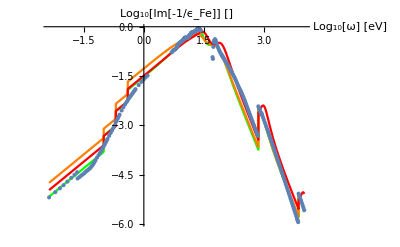

```mathematica
If[PLOT,Show[{Plot[Log10[Sum["Ai" ELFM0[10^ω("JpereV")/("ℏ")/.SIcrustparams ,"νi","ωi"]HeavisideTheta[("JpereV")/("ℏ")10^ω-"ωedgei"]/.FeTotalparams[[i]],{i,Length[FeTotalparams]}]],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotStyle->Green,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]] []"],Plot[Log10[Sum["Ai" ELFM0[10^ω("JpereV")/("ℏ")/.SIConstRepl ,"νi","ωi"]HeavisideTheta[("JpereV")/("ℏ")10^ω-"ωedgei"]/.FeTotalparamsExtrapolatedν[[i]],{i,Length[FeTotalparamsExtrapolatedν]}]],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotStyle->Orange,PlotLabel->"Log_10[Im[-1/ϵ_Fe]] [] - Extrapolated ν"],
Plot[Log10[Sum["Ai" ELFM0[10^ω("JpereV")/("ℏ")/.SIConstRepl ,"νi","ωi"]HeavisideTheta[("JpereV")/("ℏ")10^ω-"ωedgei"]/.FeTotalparamsExtrapolatedνn[[i]],{i,Length[FeTotalparamsExtrapolatedνn]}]],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotStyle->Red,PlotLabel->"Log_10[Im[-1/ϵ_Fe]] [] - Extrapolated ν n"],ListPlot[Log10[SortBy[ELFFeData,First]]]}]]
```

#### Rescale Iron parameters according to Truncation Results

-Graphics-

```mathematica
Aratio1to4 = Table[Join[{{2^-1,Aofq[2^-1,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{1.5,Aofq[1.5,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{3,Aofq[3,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])}},Table[{2 i,Aofq[2 i,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{i,1,50}]],{j,4}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {783.193}. NIntegrate obtained 0.866634 and 1.22455×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {3.11371}. NIntegrate obtained 0.0963226 and 2.6551×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {4.38473}. NIntegrate obtained 0.0240824 and 9.80383×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

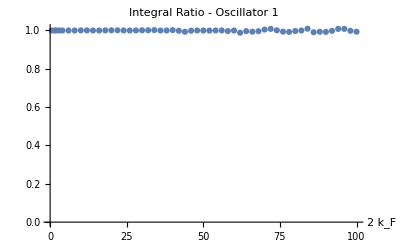

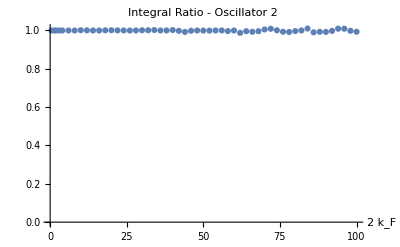

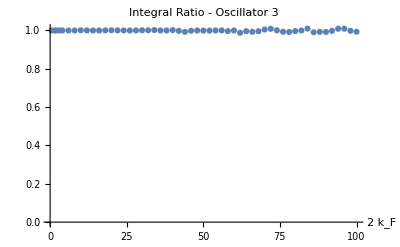

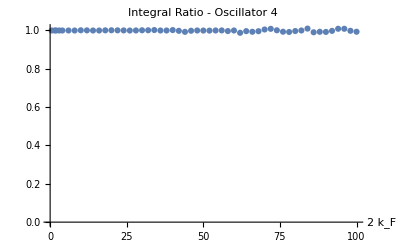

```mathematica
Do[Print[ListPlot[Aratio1to4[[i]],PlotRange->{0,1.01},PlotLabel->StringForm["Integral Ratio - Oscillator ``",ToString[i]],AxesLabel->{"2 k_F"}]],{i,4}]
```

```mathematica
Aratio56 = Table[Join[{{2^-1,Aofq[2^-1,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{1.5,Aofq[1.5,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{3,Aofq[3,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])}},Table[{2 i,Aofq[2 i,FeTotalparams[[j]]]/("Ai"/.FeTotalparams[[j]])},{i,1,50}]],{j,5,6}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {1.92918}. NIntegrate obtained 0.0543435 and 8.11288×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {3.16426}. NIntegrate obtained 0.00607002 and 2.6047×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in OpticalFits`Private`u near {OpticalFits`Private`u} = {4.40997}. NIntegrate obtained 0.00151745 and 1.53183×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

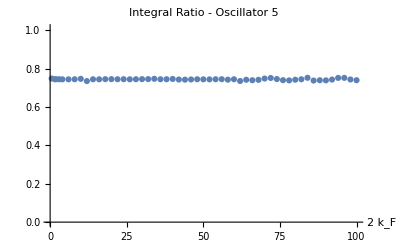

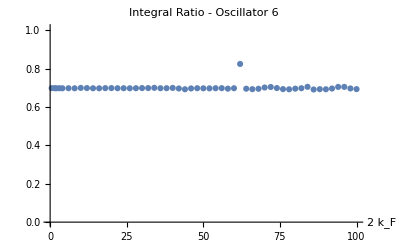

```mathematica
ListPlot[Aratio56[[1]],PlotRange->{0,1.01},PlotLabel->StringForm["Integral Ratio - Oscillator ``",ToString[5]],AxesLabel->{"2 k_F"}]
ListPlot[Aratio56[[2]],PlotRange->{0,1.01},PlotLabel->StringForm["Integral Ratio - Oscillator ``",ToString[6]],AxesLabel->{"2 k_F"}]
```

```mathematica
FeTotalparams[[5]]=RescaleAi[FeTotalparams[[5]],0.75]
FeTotalparams[[6]]=RescaleAi[FeTotalparams[[6]],0.70]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18}

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}

```mathematica
FeTotalparamsExtrapolatedν[[5]]=RescaleAi[FeTotalparamsExtrapolatedν[[5]],0.75]
FeTotalparamsExtrapolatedν[[6]]=RescaleAi[FeTotalparamsExtrapolatedν[[6]],0.70]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.55522×10^17,Ai→0.00108607,ωedgei→1.09042×10^18}

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.23434×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}

```mathematica
FeTotalparamsExtrapolatedνn[[5]]=RescaleAi[FeTotalparamsExtrapolatedνn[[5]],0.75]
FeTotalparamsExtrapolatedνn[[6]]=RescaleAi[FeTotalparamsExtrapolatedνn[[6]],0.70]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→6.91658×10^32,qF→2.73592×10^11,vF→3.16839×10^7,μ→4.57262×10^-16,ωp→1.48463×10^18,α→1/137,χ→0.148322,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→6053.18,nI→8.64572×10^31,Z→8,M→9.27329×10^-26,EF→4.57262×10^-16,ωi→1.48463×10^18,νi→7.55522×10^17,Ai→0.00108607,ωedgei→1.09042×10^18}

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→6.66733×10^34,qF→1.25446×10^12,vF→1.45275×10^8,μ→9.61328×10^-15,ωp→1.45763×10^19,α→1/137,χ→0.0692675,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→127260.,nI→8.33416×10^33,Z→8,M→9.27329×10^-26,EF→9.61328×10^-15,ωi→1.45763×10^19,νi→5.23434×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}

#### Save parameters

```mathematica
SaveIt[NotebookDirectory[]<>"FeTotalparams",FeTotalparams]
SaveIt[NotebookDirectory[]<>"FeTotalparamsExtrapolatedν",FeTotalparamsExtrapolatedν]
SaveIt[NotebookDirectory[]<>"FeTotalparamsExtrapolatedνn",FeTotalparamsExtrapolatedνn]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\ELandKappamin\extract optical data\FeTotalparams.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\ELandKappamin\extract optical data\FeTotalparamsExtrapolatedν.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\ELandKappamin\extract optical data\FeTotalparamsExtrapolatedνn.dat